# Walsh functions and lossy compression.

Walsh functions are best introduced via Hadamard matrices.

## Hadamard matrices :

```mathematica
Clear[H];H[0]=1;
```

```mathematica
H[k_]:=H[k]=ArrayFlatten[{{H[k-1],H[k-1]},{H[k-1],-H[k-1]}}]
```

```mathematica
Table[Print["H[",j,"]=",H[j]//MatrixForm],{j,1,4}]
```

H[1]=(1 | 1
1 | -1)

H[2]=(1 | 1 | 1 | 1
1 | -1 | 1 | -1
1 | 1 | -1 | -1
1 | -1 | -1 | 1)

H[3]=(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1)

H[4]=(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1)

## Walsh-1D functions :

Walsh functions are given by the rows (equivalently the columns) of the Hadamard matrices.

```mathematica
Walsh1D[s_,j_]:=H[s][[j]]
```

Two examples : s = 3 (8 functions) and s = 4 (16 functions) :

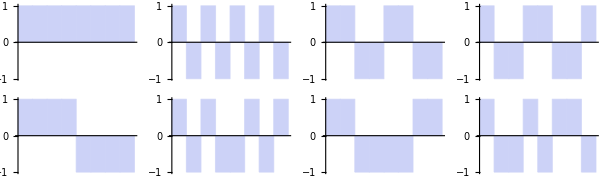

```mathematica
GraphicsGrid[Partition[Table[Show[BarChart[Walsh1D[3,j],BarSpacing->None],PlotRange->{-1,1}],{j,8}],4]]
```

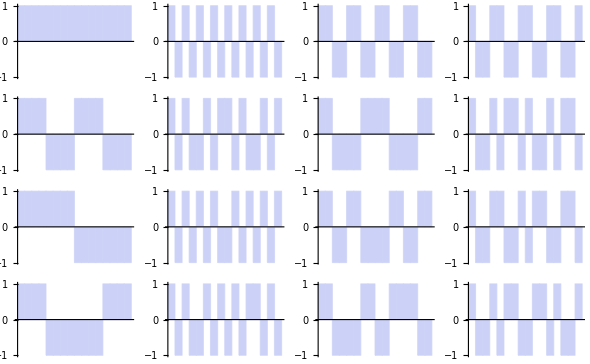

```mathematica
GraphicsGrid[Partition[Table[Show[BarChart[Walsh1D[4,j],BarSpacing->None],PlotRange->{-1,1}],{j,16}],4]]
```

Walsh functions are orthonormed with respect to the following scalar product :

```mathematica
a_⊙b_:=Total[a b,2]
```

```mathematica
Table[(2^(-3/2)Walsh1D[3,i])⊙(2^(-3/2)Walsh1D[3,j]),{i,8},{j,8}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

An arbitrary binary 1D-function (say {1,1,1,1,1,1,-1,-1} if s = 3)  is expandable in the basis of 1D-Walsh functions :

```mathematica
{1,1,1,1,1,1,-1,-1}==∑_(j=1)^8 ((2^(-3/2)Walsh1D[3,j])⊙{1,1,1,1,1,1,-1,-1})(2^(-3/2)Walsh1D[3,j])
```

True

## Walsh-2D functions :

```mathematica
Walsh2D[s_,i_,j_]:=Outer[Times,Walsh1D[s,i],Walsh1D[s,j]]
```

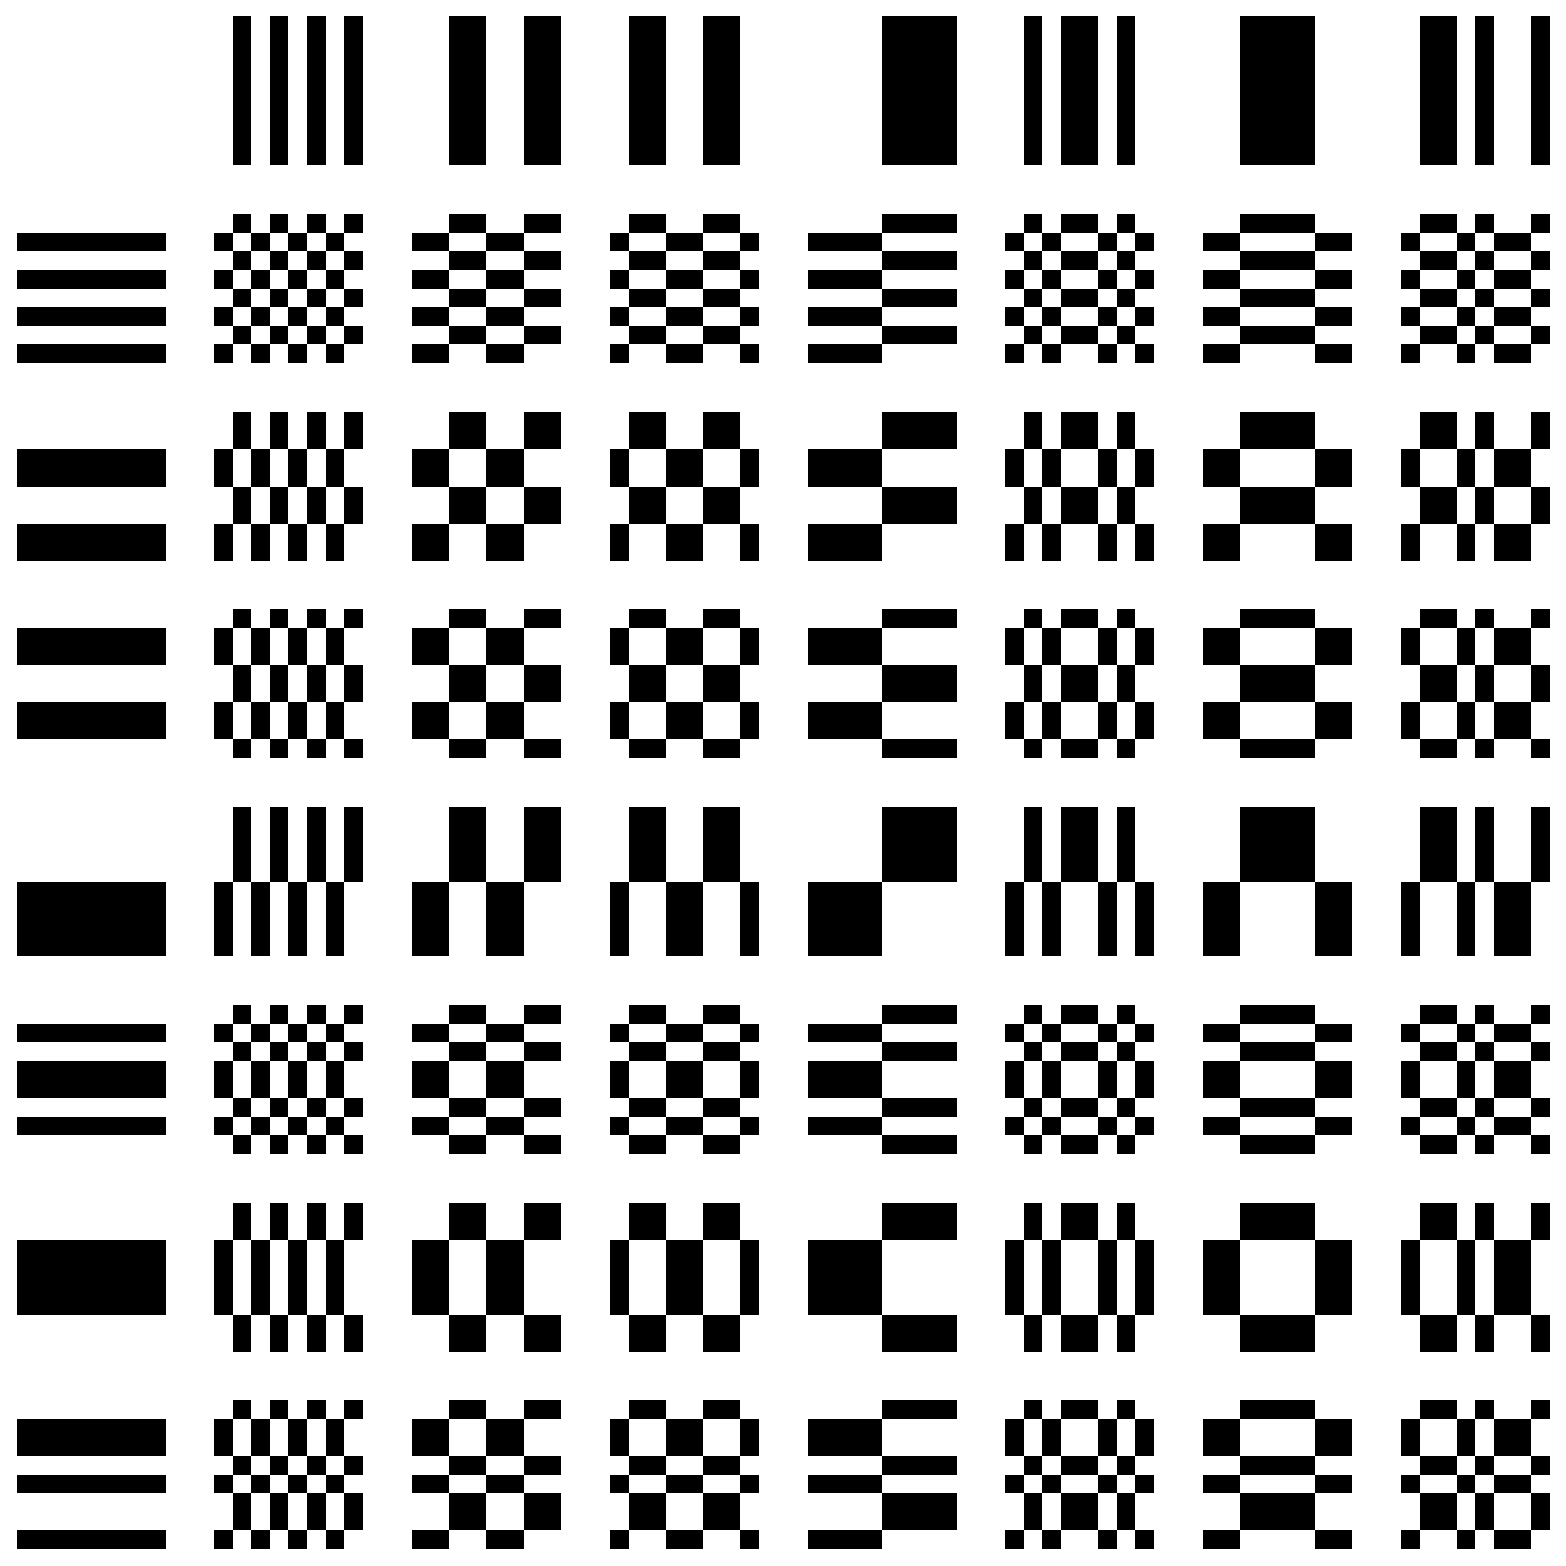

```mathematica
GraphicsGrid[Table[ArrayPlot[Walsh2D[3,i,j],ColorRules->{-1->Black,1->White}],{i,8},{j,8}]]
```

The following character, R, is pixellized in a 64x64 grid :

```mathematica
Rpixels=ImageData[-Graphics-,"Bit"]/.{{1,1,1}->1,{0,0,0}->-1};
```

```mathematica
Rpixels//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
Image[ Rpixels]
```

-Graphics-

```mathematica
coefficientsR[i_,j_]:=Walsh2D[6,i,j]⊙Rpixels
```

The walsh coefficients for the letter R :

```mathematica
Table[coefficientsR[i,j],{i,1,64},{j,1,64}]
```

{{3004,-68,-52,-68,-184,104,128,48,-144,-56,-40,-64,-140,12,-28,76,64,64,80,64,204,-20,4,-76,500,76,92,68,248,-112,-152,-48,-60,-60,-76,-60,-200,24,0,80,-496,-72,-88,-64,-244,116,156,52,1088,64,48,64,180,-108,-132,-52,140,52,36,60,136,-16,24,-80},{8,8,8,-8,12,12,-12,4,-4,-12,4,12,8,0,-8,0,4,4,4,-12,8,8,-16,0,-8,-16,0,8,4,-4,-12,-4,-8,-8,-8,8,-12,-12,12,-4,4,12,-4,-12,-8,0,8,0,-4,-4,-4,12,-8,-8,16,0,8,16,0,-8,-4,4,12,4},{8,8,-24,8,12,-4,-12,4,4,-4,12,4,0,8,16,-8,4,4,-28,4,8,-8,-16,0,0,-8,8,0,-4,4,12,-12,-8,-8,24,-8,-12,4,12,-4,-4,4,-12,-4,0,-8,-16,8,-4,-4,28,-4,-8,8,16,0,0,8,-8,0,4,-4,-12,12},{-4,-4,-4,-4,8,-8,16,0,-24,0,0,-8,-4,4,-4,4,0,0,0,0,12,-4,20,4,-20,4,4,-4,0,8,0,8,4,4,4,4,-8,8,-16,0,24,0,0,8,4,-4,4,-4,0,0,0,0,-12,4,-20,-4,20,-4,-4,4,0,-8,0,-8},{80,-8,-8,-16,20,12,20,-4,20,-12,-12,4,-80,0,8,8,-4,4,4,-4,48,8,16,-8,64,0,0,16,-52,-4,4,4,8,0,0,8,-44,-4,-12,12,-60,4,4,-12,56,8,0,0,-84,4,4,12,-24,-16,-24,0,-24,8,8,-8,76,-4,-12,-12},{-76,12,-4,4,-16,-8,-16,8,24,8,8,8,28,-4,4,-12,8,0,-16,-8,-44,-4,-12,12,-20,-4,-4,-4,0,0,8,-8,-12,-4,12,4,40,0,8,-16,16,0,0,0,-4,-4,-12,4,80,-8,8,0,20,12,20,-4,-20,-4,-4,-4,-24,8,0,16},{-84,4,20,-20,-24,0,-24,0,24,8,8,24,44,-4,-12,4,0,-8,8,-32,-52,4,-20,4,-20,-4,-4,12,16,0,-8,8,-4,4,-12,28,48,-8,16,-8,16,0,0,-16,-20,-4,4,-12,88,0,-16,24,28,4,28,4,-20,-4,-4,-20,-40,8,16,0},{40,-16,0,8,-20,-12,-4,4,4,4,20,-12,16,16,-8,-8,-44,-4,12,20,8,-16,-8,0,48,16,32,0,44,12,-12,-12,48,8,-8,-16,-4,20,12,4,-44,-12,-28,4,-40,-8,16,16,-44,12,-4,-12,16,8,0,-8,-8,-8,-24,8,-20,-20,4,4},{68,12,12,-12,56,-16,-40,-16,-48,-16,0,0,-36,12,36,20,-16,24,24,0,84,-20,-44,-20,-4,-4,12,12,-8,8,32,16,20,-20,-20,4,-80,24,48,24,8,8,-8,-8,12,-4,-28,-12,-72,-16,-16,8,-60,12,36,12,44,12,-4,-4,32,-16,-40,-24},{-80,8,-8,16,-4,4,-4,4,12,-4,12,-4,32,0,-8,-8,4,-4,-20,4,-32,8,0,8,-32,-16,0,-16,4,4,-4,-4,-8,0,16,-8,28,-12,-4,-12,28,12,-4,12,-8,-8,0,0,84,-4,12,-12,8,0,8,0,-8,8,-8,8,-28,4,12,12},{-88,0,0,8,4,-4,-12,-4,-4,12,12,12,48,0,-8,-8,-4,-12,-12,-4,-24,0,-8,0,-48,0,0,0,20,4,-4,-4,0,8,8,0,20,-4,4,-4,44,-4,-4,-4,-24,-8,0,0,92,4,4,-4,0,8,16,8,8,-8,-8,-8,-44,4,12,12},{44,-12,-12,-20,-16,-8,-16,8,0,0,16,0,12,12,20,4,-40,0,0,-8,12,-12,-20,4,44,12,28,12,40,8,16,0,44,4,4,12,-8,16,24,0,-40,-8,-24,-8,-36,-4,-12,4,-48,8,8,16,12,4,12,-12,-4,-4,-20,-4,-16,-16,-24,-8},{-440,-24,-8,24,-28,4,28,-4,-76,12,12,-28,8,0,-24,0,76,-20,-4,28,-24,8,32,0,-72,16,16,-24,12,4,-20,4,-72,24,8,-24,28,-4,-28,4,76,-12,-12,28,-8,0,24,0,436,20,4,-28,24,-8,-32,0,72,-16,-16,24,-12,-4,20,-4},{12,12,12,12,0,0,8,8,8,0,0,-8,4,-4,-28,-4,8,8,8,8,-4,-4,4,4,4,-4,-4,-12,0,-8,-32,-8,-12,-12,-12,-12,0,0,-8,-8,-8,0,0,8,-4,4,28,4,-8,-8,-8,-8,4,4,-4,-4,-4,4,4,12,0,8,32,8},{12,12,-4,12,-16,0,8,8,32,-8,8,-16,-4,4,-20,4,8,8,-8,8,-20,-4,4,4,28,-12,4,-20,-8,0,-24,0,-12,-12,4,-12,16,0,-8,-8,-32,8,-8,16,4,-4,20,-4,-8,-8,8,-8,20,4,-4,-4,-28,12,-4,20,8,0,24,0},{-8,-8,8,-8,4,-12,-4,-4,-20,4,4,12,0,8,0,-8,-4,-4,12,-4,8,-8,0,0,-16,8,8,16,4,12,4,-4,8,8,-8,8,-4,12,4,4,20,-4,-4,-12,0,-8,0,8,4,4,-12,4,-8,8,0,0,16,-8,-8,-16,-4,-12,-4,4},{-184,-8,-16,32,-68,-36,-36,28,-124,44,52,-4,176,8,24,-48,76,-36,-44,4,-144,-16,-16,48,-248,16,24,-32,100,28,44,-28,-80,32,40,-8,140,12,12,-52,244,-20,-28,28,-104,-32,-48,24,188,12,20,-28,72,40,40,-24,128,-40,-48,8,-172,-4,-20,52},{-52,-4,-12,4,-8,-8,-8,-8,-8,0,-8,0,12,4,4,-4,40,-8,-16,0,-28,4,4,4,-44,-4,-12,-4,-8,16,16,8,-36,12,20,4,32,0,0,0,48,8,16,8,12,-12,-12,-4,48,0,8,-8,4,4,4,4,4,-4,4,-4,-16,-8,-8,0},{-52,-4,-12,20,8,-8,-24,8,-32,8,0,-8,20,-4,12,-28,40,-8,-16,16,-12,4,-12,20,-68,4,-4,-12,0,8,24,-16,-36,12,20,-12,16,0,16,-16,72,0,8,16,4,-4,-20,20,48,0,8,-24,-12,4,20,-12,28,-12,-4,4,-24,0,-16,24},{56,8,-16,-16,-4,12,12,12,12,-12,12,4,-8,0,16,8,-36,12,-12,-12,16,0,0,0,48,-8,16,8,12,-12,4,-4,32,-16,8,8,-20,-4,-4,-4,-52,4,-20,-12,-16,8,-8,0,-52,-4,20,20,8,-8,-8,-8,-8,16,-8,0,12,4,-12,-4},{180,12,4,-4,16,-24,-24,0,0,16,24,40,52,4,20,-28,16,-24,-32,-40,-84,4,4,28,-164,-20,-12,4,-48,32,48,0,-20,20,28,36,80,-8,-8,-32,160,16,8,-8,44,-36,-52,-4,-176,-8,0,8,-12,28,28,4,4,-12,-20,-36,-48,0,-16,32},{0,-24,0,8,-12,-4,-4,4,28,28,-12,-12,-8,-8,-8,-8,4,-20,4,12,-8,0,0,8,32,32,-8,-8,-4,-4,-4,-4,0,24,0,-8,12,4,4,-4,-28,-28,12,12,8,8,8,8,-4,20,-4,-12,8,0,0,-8,-32,-32,8,8,4,4,4,4},{8,-16,8,0,-20,4,20,-4,44,12,-28,-12,-24,-8,-24,8,12,-12,12,4,-16,8,24,0,48,16,-24,-8,-20,-4,-20,12,-8,16,-8,0,20,-4,-20,4,-44,-12,28,12,24,8,24,-8,-12,12,-12,-4,16,-8,-24,0,-48,-16,24,8,20,4,20,-12},{-20,4,12,20,-8,0,0,-8,16,0,-8,-8,4,4,20,4,-24,0,8,16,-12,-4,-4,-12,12,-4,-12,-12,0,0,16,0,20,-4,-12,-20,8,0,0,8,-16,0,8,8,-4,-4,-20,-4,24,0,-8,-16,12,4,4,12,-12,4,12,12,0,0,-16,0},{168,16,24,16,36,-52,-68,-12,-68,28,36,20,112,16,32,-16,4,-20,-12,-20,-64,-24,-40,16,-232,-8,0,-16,12,44,60,12,-8,16,8,16,60,20,36,-20,228,4,-4,12,-16,-48,-64,-16,-164,-12,-20,-12,-32,56,72,16,72,-24,-32,-16,-108,-12,-28,20},{-4,-12,-4,4,16,8,-8,0,16,0,-8,-8,-20,-4,-4,-4,0,-8,0,8,20,12,-4,4,20,4,-4,-4,-16,0,0,0,4,12,4,-4,-16,-8,8,0,-16,0,8,8,20,4,4,4,0,8,0,-8,-20,-12,4,-4,-20,-4,4,4,16,0,0,0},{4,-4,-12,12,24,0,16,-8,16,0,-24,-8,-36,-4,-4,-4,8,0,-8,16,28,4,20,-4,20,4,-20,-4,-32,0,0,0,-4,4,12,-12,-24,0,-16,8,-16,0,24,8,36,4,4,4,-8,0,8,-16,-28,-4,-20,4,-20,-4,20,4,32,0,0,0},{-16,-8,0,8,-20,4,4,-4,12,12,-12,-12,16,0,32,16,-20,-12,-4,4,-24,0,0,-8,8,8,-16,-16,12,-4,28,12,16,8,0,-8,20,-4,-4,4,-12,-12,12,12,-16,0,-32,-16,20,12,4,-4,24,0,0,8,-8,-8,16,16,-12,4,-28,-12},{-172,20,28,12,72,-8,8,-24,-56,0,-24,16,-44,-4,12,4,88,-8,0,-16,-4,12,28,-4,-180,-28,-52,-12,-120,16,32,24,-92,4,-4,12,0,-16,-32,0,176,24,48,8,116,-20,-36,-28,176,-16,-24,-8,-68,12,-4,28,60,4,28,-12,48,8,-8,0},{-48,16,-8,8,-4,-20,-4,-4,4,-4,-12,-4,-8,0,0,-8,44,12,-12,4,-24,-8,8,8,-32,-8,-16,-8,-28,12,12,4,-40,-8,16,0,28,12,-4,-4,36,12,20,12,32,-8,-8,0,44,-20,4,-12,0,16,0,0,-8,0,8,0,4,-4,-4,4},{-48,16,8,8,-4,-4,-20,12,-4,-12,-4,-12,0,-8,-8,-16,44,12,4,4,-24,8,-8,24,-40,-16,-8,-16,-20,4,4,-4,-40,-8,0,0,28,-4,12,-20,44,20,12,20,24,0,0,8,44,-20,-12,-12,0,0,16,-16,0,8,0,8,-4,4,4,12},{52,-12,-4,-4,-24,8,8,8,16,8,16,8,12,4,4,-4,-40,-8,0,0,-4,-4,-4,-4,52,12,20,12,32,-8,-8,-16,36,4,-4,-4,0,0,0,0,-56,-16,-24,-16,-36,4,4,12,-48,16,8,8,28,-4,-4,-4,-12,-4,-12,-4,-8,0,0,8},{-88,8,16,0,28,12,12,-20,52,-4,-12,12,-32,-8,-24,16,-4,-4,4,-12,0,16,16,-16,8,-16,-24,0,-60,-4,-20,20,0,0,-8,8,-4,-20,-20,12,-12,12,20,-4,56,0,16,-24,92,-4,-12,4,-24,-8,-8,24,-48,8,16,-8,36,12,28,-12},{68,4,12,-4,16,0,0,0,-16,-8,0,-8,-28,-4,-4,4,-16,16,24,8,44,-4,-4,-4,28,4,12,4,0,-8,-8,0,20,-12,-20,-4,-40,8,8,8,-24,0,-8,0,4,12,12,4,-72,-8,-16,0,-20,-4,-4,-4,12,4,-4,4,24,0,0,-8},{76,-4,4,-12,8,-8,8,-8,0,-8,0,-8,-44,12,-4,20,-8,8,16,0,36,-12,4,-12,44,4,12,4,-16,8,-8,16,12,-4,-12,4,-32,16,0,16,-40,0,-8,0,20,-4,12,-12,-80,0,-8,8,-12,4,-12,4,-4,4,-4,4,40,-16,0,-24},{-48,0,24,8,20,4,4,-12,-12,12,-12,12,0,-8,-24,0,36,-12,12,-4,-8,8,8,-8,-56,0,-24,0,-28,-4,-20,4,-40,8,-16,0,4,-12,-12,4,52,-4,20,-4,24,0,16,-8,52,4,-20,-4,-16,0,0,16,16,-8,16,-8,4,12,28,4},{412,4,12,36,24,0,0,-8,88,8,0,-32,12,-4,-20,12,-104,0,8,32,20,-4,-4,-12,84,4,-4,-36,8,-8,-24,8,100,-4,-12,-36,-24,0,0,8,-88,-8,0,32,-12,4,20,-12,-408,0,-8,-32,-20,4,4,12,-84,-4,4,36,-8,8,24,-8},{-16,8,-16,-8,4,-4,-4,4,-20,-20,20,4,8,8,8,-8,-12,12,-12,-4,8,0,0,8,-16,-16,24,8,12,12,12,-4,16,-8,16,8,-4,4,4,-4,20,20,-20,-4,-8,-8,-8,8,12,-12,12,4,-8,0,0,-8,16,16,-24,-8,-12,-12,-12,4},{-32,8,-16,-8,4,-4,-20,4,-28,-12,28,12,32,0,16,-16,-28,12,-12,-4,8,0,-16,8,-24,-8,32,16,36,4,20,-12,32,-8,16,8,-4,4,20,-4,28,12,-28,-12,-32,0,-16,16,28,-12,12,4,-8,0,16,-8,24,8,-32,-16,-36,-4,-20,12},{12,4,-4,-12,-8,0,0,8,0,0,8,8,20,4,-12,4,8,0,-8,-16,-12,-4,-4,4,-4,-4,4,4,16,0,-16,0,-12,-4,4,12,8,0,0,-8,0,0,-8,-8,-20,-4,12,-4,-8,0,8,16,12,4,4,-4,4,4,-4,-4,-16,0,16,0},{424,0,-8,16,4,28,44,4,156,-4,-12,-12,-48,-16,-32,0,-92,-4,-12,12,0,24,40,0,152,-8,-16,-16,-52,-20,-36,-4,88,0,8,-16,-4,-28,-44,-4,-156,4,12,12,48,16,32,0,-420,4,12,-12,0,-24,-40,0,-152,8,16,16,52,20,36,4},{-12,-4,-12,-4,-24,-16,0,8,-8,8,16,0,20,4,4,-12,-8,0,-8,0,-20,-12,4,12,-4,12,20,4,24,8,8,-8,12,4,12,4,24,16,0,-8,8,-8,-16,0,-20,-4,-4,12,8,0,8,0,20,12,-4,-12,4,-12,-20,-4,-24,-8,-8,8},{-28,-4,4,-20,-40,0,-16,8,0,0,24,8,44,-4,-4,-4,-24,0,8,-16,-36,4,-12,12,4,4,28,12,48,0,0,0,28,4,-4,20,40,0,16,-8,0,0,-24,-8,-44,4,4,4,24,0,-8,16,36,-4,12,-12,-4,-4,-28,-12,-48,0,0,0},{8,16,8,0,4,-4,-4,4,4,-12,12,12,8,8,-24,-8,4,12,4,-4,0,-8,-8,0,0,-16,8,8,4,4,-28,-12,-8,-16,-8,0,-4,4,4,-4,-4,12,-12,-12,-8,-8,24,8,-4,-12,-4,4,0,8,8,0,0,16,-8,-8,-4,-4,28,12},{-100,-20,-28,20,-112,-16,-32,32,-16,40,64,-8,188,4,-12,-36,-16,-32,-40,8,-140,-12,-28,36,-60,28,52,-20,160,8,-8,-32,12,28,36,-12,136,8,24,-40,56,-32,-56,16,-164,-12,4,28,104,24,32,-16,116,20,36,-28,20,-36,-60,12,-184,0,16,40},{64,-16,8,-8,12,12,-4,-4,-28,-4,4,-4,-8,0,0,8,-20,-4,20,4,40,8,-8,-8,16,8,16,8,20,-4,-4,4,24,8,-16,0,-36,-4,12,12,-12,-4,-12,-4,-16,8,8,0,-68,12,-12,4,-16,-16,0,0,24,0,-8,0,4,-4,-4,-12},{72,-24,-16,0,20,-12,4,-12,-28,12,4,-4,-24,16,16,8,-12,-12,-4,12,48,-16,0,-16,16,24,16,8,4,12,12,4,16,16,8,-8,-44,20,4,20,-12,-20,-12,-4,0,-8,-8,0,-76,20,12,-4,-24,8,-8,8,24,-16,-8,0,20,-20,-20,-12},{-44,20,12,-4,40,8,8,-8,-16,-8,-16,8,-20,-12,-12,12,40,8,0,-16,12,12,12,-4,-60,-20,-28,-4,-48,-8,-8,16,-44,-12,-4,12,-16,-16,-16,0,56,16,24,0,44,4,4,-20,48,-16,-8,8,-36,-4,-4,12,20,12,20,-4,24,16,16,-8},{500,52,36,36,144,-80,-104,-40,56,32,16,56,76,-12,28,-60,24,-40,-56,-56,-140,20,-4,60,-420,-60,-76,-36,-208,88,128,40,-20,44,60,60,144,-16,8,-56,424,64,80,40,212,-84,-124,-36,-504,-56,-40,-40,-148,76,100,36,-60,-36,-20,-60,-80,8,-32,56},{8,8,8,8,-4,-4,20,-12,-4,4,-12,-4,-8,0,8,16,4,4,4,4,-8,-8,16,-16,-8,0,-16,-8,-12,-4,4,12,-8,-8,-8,-8,4,4,-20,12,4,-4,12,4,8,0,-8,-16,-4,-4,-4,-4,8,8,-16,16,8,0,16,8,12,4,-4,-12},{16,0,32,0,4,4,12,-4,-20,4,-12,-4,-8,0,-8,16,12,-4,28,-4,0,0,8,-8,-24,0,-16,-8,-12,-4,-12,12,-16,0,-32,0,-4,-4,-12,4,20,-4,12,4,8,0,8,-16,-12,4,-28,4,0,0,-8,8,24,0,16,8,12,4,12,-12},{12,-4,-4,-4,8,8,-16,0,8,0,0,8,-20,-12,-4,-12,16,0,0,0,12,12,-12,4,12,4,4,12,-16,-8,0,-8,-12,4,4,4,-8,-8,16,0,-8,0,0,-8,20,12,4,12,-16,0,0,0,-12,-12,12,-4,-12,-4,-4,-12,16,8,0,8},{192,8,8,-16,20,12,4,-4,52,-28,-28,-12,-64,0,-8,24,-68,36,36,12,96,-8,-16,-24,176,0,0,16,12,-20,-28,4,72,-32,-32,-8,-92,12,20,28,-172,4,4,-12,-8,24,32,0,-196,-12,-12,12,-24,-16,-8,0,-56,24,24,8,60,-4,4,-28},{60,-12,4,-4,8,16,24,0,0,0,0,0,-12,4,-4,12,-32,-8,8,0,28,4,12,-12,36,4,4,4,8,-8,-16,0,28,4,-12,-4,-32,-8,-16,8,-40,-8,-8,-8,-12,4,12,-4,-56,16,0,8,-4,-12,-20,4,4,4,4,4,16,0,8,-8},{60,4,-12,12,8,16,40,0,8,-8,-8,-8,-20,-4,4,4,-32,8,-8,16,28,4,28,-12,44,-4,-4,-4,0,-16,-8,-8,28,-12,4,-20,-32,-8,-32,8,-48,0,0,0,-4,12,4,4,-56,0,16,-8,-4,-12,-36,4,-4,12,12,12,24,8,0,0},{-48,8,-8,0,4,-4,-12,-4,-4,-4,-20,-4,-8,-8,16,0,44,4,-12,-4,-16,8,0,8,-40,-8,-24,-8,-28,4,28,12,-40,0,16,8,20,-4,4,-4,44,12,28,12,32,0,-24,-8,44,-12,4,-4,-8,0,8,0,0,0,16,0,4,4,-20,-4},{204,-12,-12,-20,-16,40,64,8,120,-24,-40,-8,-108,-12,-36,12,-56,16,16,8,60,20,44,-12,244,4,-12,20,-32,-32,-56,-8,60,-12,-12,-4,-56,-16,-40,16,-240,0,16,-16,36,36,60,12,-208,8,8,16,12,-44,-68,-12,-124,20,36,4,104,8,32,-16},{64,-8,8,-16,-4,4,12,4,12,12,-4,12,-16,0,8,8,-28,-4,12,-12,16,-8,0,-8,48,16,0,16,4,-12,-4,-4,24,0,-16,8,-20,4,-4,4,-52,-20,-4,-20,-8,8,0,0,-60,12,-4,20,8,0,-8,0,-8,-8,8,-8,20,4,-4,-4},{64,8,8,-16,-20,20,28,4,36,-12,-12,4,-24,-8,0,16,-28,12,12,-12,0,8,16,-8,72,-8,-8,8,-4,-20,-12,4,24,-16,-16,8,-4,-12,-20,4,-76,4,4,-12,0,16,8,-8,-60,-4,-4,20,24,-16,-24,0,-32,16,16,0,28,12,4,-12},{-52,4,4,28,0,-8,0,-8,0,0,-16,-16,-4,-4,-12,-12,40,0,0,24,-20,4,12,4,-36,-4,-20,-20,-24,8,0,0,-36,4,4,-20,24,0,-8,0,40,8,24,24,28,-4,4,4,48,-8,-8,-32,-4,4,-4,4,-4,-4,12,12,0,0,8,8},{-152,8,-8,-56,-12,20,-4,12,-12,-36,-36,20,-72,0,24,16,12,44,28,-20,88,-8,-32,-16,152,0,0,56,28,-28,-4,-12,-8,-40,-24,24,-84,12,36,20,-148,4,4,-52,-24,32,8,16,148,-12,4,52,8,-24,0,-16,8,32,32,-24,68,-4,-28,-20},{4,4,4,-12,8,8,0,-16,-16,-8,-8,16,-4,4,28,20,0,0,0,-16,4,4,-4,-20,-20,-12,-12,12,-8,0,24,16,-4,-4,-4,12,-8,-8,0,16,16,8,8,-16,4,-4,-28,-20,0,0,0,16,-4,-4,4,20,20,12,12,-12,8,0,-24,-16},{12,-4,12,-4,32,0,-8,-8,-48,8,-8,16,-4,4,28,4,8,-8,8,-8,28,-4,-12,-12,-52,4,-12,12,-8,0,24,0,-12,4,-12,4,-32,0,8,8,48,-8,8,-16,4,-4,-28,-4,-8,8,-8,8,-28,4,12,12,52,-4,12,-12,8,0,-24,0},{16,0,-16,0,12,12,4,4,4,-4,-4,-12,-24,-16,-8,0,20,4,-12,4,16,16,8,8,8,0,0,-8,-20,-12,-4,4,-16,0,16,0,-12,-12,-4,-4,-4,4,4,12,24,16,8,0,-20,-4,12,-4,-16,-16,-8,-8,-8,0,0,8,20,12,4,-4}}

The walsh coefficients for the letter R, sorted in decreasing order (absolute value) :

```mathematica
Sort[Flatten[Table[Abs[coefficientsR[i,j]],{i,1,64},{j,1,64}]],Greater]
```

{3004,1088,504,500,500,496,440,436,424,424,420,420,412,408,248,248,244,244,244,240,232,228,212,208,208,204,204,200,196,192,188,188,184,184,184,180,180,180,176,176,176,176,176,172,172,172,168,164,164,164,160,160,156,156,156,152,152,152,152,152,148,148,148,144,144,144,144,140,140,140,140,140,136,136,132,128,128,128,124,124,124,120,120,116,116,116,112,112,112,108,108,108,104,104,104,104,104,104,100,100,100,100,96,92,92,92,92,92,92,88,88,88,88,88,88,88,88,88,88,84,84,84,84,84,84,84,84,84,80,80,80,80,80,80,80,80,80,80,80,80,80,80,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,68,68,68,68,68,68,68,68,68,68,68,68,68,68,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

An arbitrary binary 2D-function (say Rpixels)  is expandable without loss in the basis of 2D-Walsh functions :

```mathematica
Image[Sum[coefficientsR[i,j]Walsh2D[6,i,j],{i,64},{j,64}]/4096]
```

-Graphics-

```mathematica
64*64
```

4096

Light truncation :

```mathematica
Image[Sum[If[Abs[coefficientsR[i,j]]>20,coefficientsR[i,j],0]Walsh2D[6,i,j],{i,64},{j,64}]/4096]
```

-Graphics-

```mathematica
Length[Select[Flatten[Table[coefficientsR[i,j],{i,64},{j,64}]],Abs[#]>20&]]
```

872

Light truncation with greylevels erased :

```mathematica
char=Sum[If[Abs[coefficientsR[i,j]]>20,coefficientsR[i,j],0]Walsh2D[6,i,j],{i,64},{j,64}]/4096
```

```mathematica
resu=Table[1,{i,64},{j,64}];Do[If[char[[i,j]]≤0,resu[[i,j]]=0,Continue],{i,64},{j,64}];
```

```mathematica
Image[resu]
```

-Graphics-

Medium truncation :

```mathematica
Image[Sum[If[Abs[coefficientsR[i,j]]>100,coefficientsR[i,j],0]Walsh2D[6,i,j],{i,64},{j,64}]/4096]
```

-Graphics-

```mathematica
Length[Select[Flatten[Table[coefficientsR[i,j],{i,64},{j,64}]],Abs[#]>100&]]
```

98

Medium truncation with greylevels erased :

```mathematica
char=Sum[If[Abs[coefficientsR[i,j]]>100,coefficientsR[i,j],0]Walsh2D[6,i,j],{i,64},{j,64}]/4096;
```

```mathematica
resu=Table[1,{i,64},{j,64}];Do[If[char[[i,j]]≤0,resu[[i,j]]=0,Continue],{i,64},{j,64}];
```

```mathematica
Image[resu]
```

-Graphics-

Strong truncation :

```mathematica
Image[Sum[If[Abs[coefficientsR[i,j]]>200,coefficientsR[i,j],0]Walsh2D[6,i,j],{i,64},{j,64}]/4096]
```

-Graphics-

```mathematica
Length[Select[Flatten[Table[coefficientsR[i,j],{i,64},{j,64}]],Abs[#]>200&]]
```

27

Strong truncation with greylevels erased :

```mathematica
char=Sum[If[Abs[coefficientsR[i,j]]>200,coefficientsR[i,j],0]Walsh2D[6,i,j],{i,64},{j,64}]/4096;
```

```mathematica
resu=Table[1,{i,64},{j,64}];Do[If[char[[i,j]]≤0,resu[[i,j]]=0,Continue],{i,64},{j,64}];
```

```mathematica
Image[resu]
```

-Graphics-